```mathematica
$Path=Prepend[$Path,"E:\\HOME\\anton\\roundabout"];
```

```mathematica
<<ACPackages`
```

```mathematica
SetWorkDir["2009-03-30"]
```

D:\Работа\Programs\torgrid-delta\2009-03-30

```mathematica
AverageTimeProfil[l_List,t_,dt_:1]:=Apply[Plus,#]/Length[#]&[Map[#[[2]]&,Select[lv,(t≤#[[1]][[1]]<t+dt)&]]];
UnsortedUnion[x_,ndig_:4]:=N[Reap[Sow[1,Round[10^ndig x]],_,#1&]⟦2⟧10^-ndig];
```

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[{#⟦1,1⟧,#⟦2⟧}&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

{2324,2.0001}

```mathematica
PrintAnim[Rest[CutList[#[[2]]&/@lv,20]]]
```

```mathematica
PrintRange[{First[#],Max[Last[#]]}&/@lv,Automatic]
```

```mathematica
Dynamic[Refresh[
len=Transpose[Import["energy.dat","Table"]];
ltm=First[len];PrintRange[dif[Union[ltm]]];
{lmp,mdp,lmvx,mdvx,lmvy,mdvy,lmvz,mdvz,lmqp,lmqvx,lmqvy,lmqvz}=Union[Transpose[{ltm,#}]]&/@Drop[len,2];
PrintRange[{#⟦1⟧/3,Log[√(#⟦2⟧)]}&/@(lmqvx+lmqvy+lmqvz)],
UpdateInterval->5]
]
```

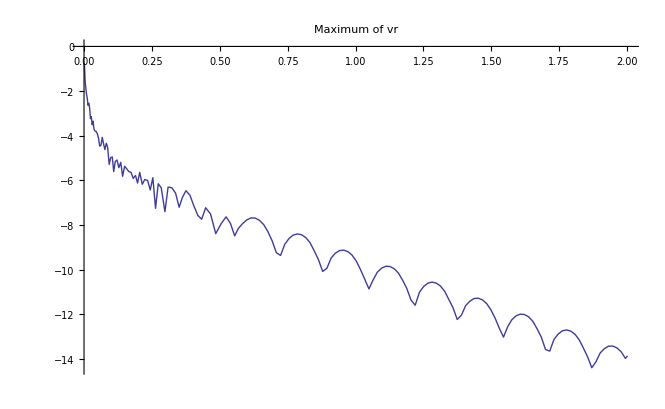
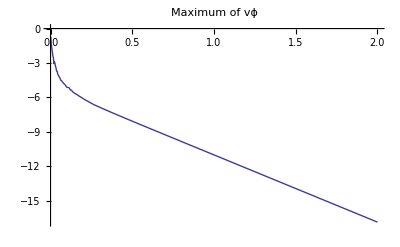
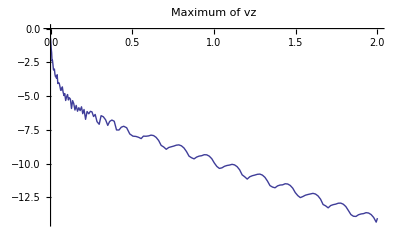
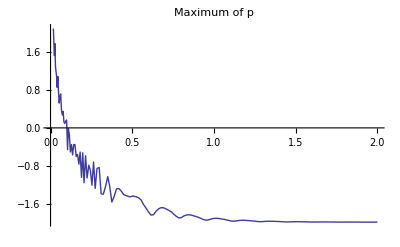

```mathematica
MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{Map[{#⟦1⟧,Log[#⟦2⟧]}&,{lmvx,lmvy,lmvz,lmp},{2}],{"Maximum of vr","Maximum of vϕ","Maximum of vz","Maximum of p"}}]
```

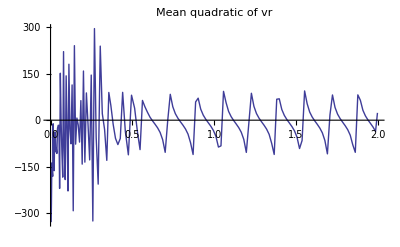
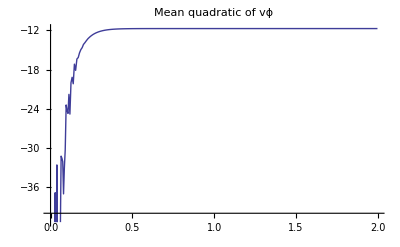
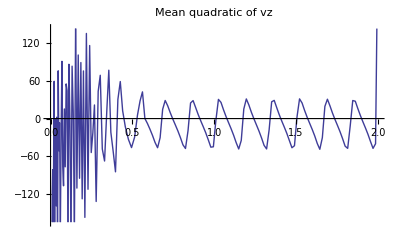
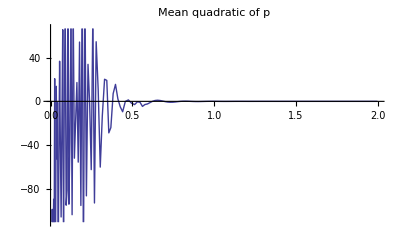

```mathematica
MapThread[PrintRange[dif@#1,Automatic,PlotLabel->#2]&,{Map[{#⟦1⟧,Log[#⟦2⟧]}&,{lmqvx,lmqvy,lmqvz,lmqp},{2}],{"Mean quadratic of vr","Mean quadratic of vϕ","Mean quadratic of vz","Mean quadratic of p"}}]
```

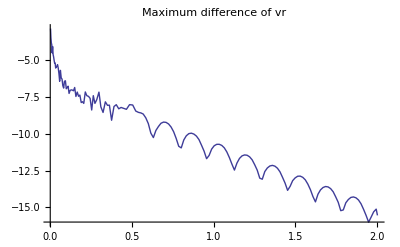
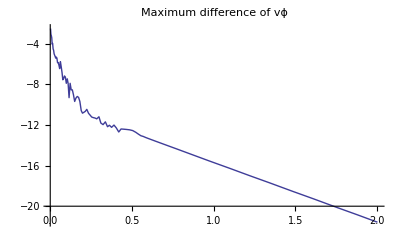
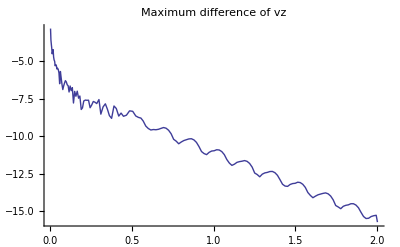
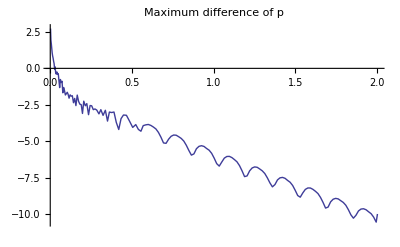

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[{#⟦1⟧,Log[#⟦2⟧]}&,{mdvx,mdvy,mdvz,mdp},{2}],{"Maximum difference of vr","Maximum difference of vϕ","Maximum difference of vz","Maximum difference of p"}}]
```

для сборки из разных файлов

```mathematica
Off[Set::write];Off[General::spell1];
Print["proc distribution:",np=Take[ReadList["runtest1_0.sta",Number],{5,7}]];
KolProc=Apply[Times,np];ghost=3;
dumpRead=Table[ReadList["shellgrid_400_"<>ToString[i]<>".snp"],{i,0,KolProc-1}];
{t,count,n1,n2,n3,Rey,vx,vy,vz,p,nut}=Transpose[dumpRead];
vx=First[Fold[Map[Function[m,Clue[m,#2]],Partition[#1,np⟦#2⟧],{1}]&,vx,{1,2,3}]];
vy=First[Fold[Map[Function[m,Clue[m,#2]],Partition[#1,np⟦#2⟧],{1}]&,vy,{1,2,3}]];
vz=First[Fold[Map[Function[m,Clue[m,#2]],Partition[#1,np⟦#2⟧],{1}]&,vz,{1,2,3}]];
p=First[Fold[Map[Function[m,Clue[m,#2]],Partition[#1,np⟦#2⟧],{1}]&,p,{1,2,3}]];
nut=First[Fold[Map[Function[m,Clue[m,#2]],Partition[#1,np⟦#2⟧],{1}]&,nut,{1,2,3}]];
Print["mesh sizes=",{n1,n2,n3}=Dimensions[vx]-2ghost];
Print["{t,count,Re}=",{t,count,Rey}=First/@{t,count,Rey}];
```

```mathematica
Remove[PrintInfo]
```

```mathematica
{p,vx,vy,vz,nut}=ReadTextSnapFile["pumpflow_2_1540.snp",5,PrintInfo->Automatic];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,1,2},NumberOfRefs->2];
Print[bounds];
```

{1,1,2}

{1.90074,1540,10,10,10,1.}

ghost=3

{{-1.,1.},{0.,1.},{-1.,1.}}

Выделение внутренней области

```mathematica
GetInner[ar_?ArrayQ]:=Block[{b},Transpose[(node/.b_:>BitAnd[b,8])/8#&/@Transpose[ar]]]
```

```mathematica
{vxs,vys,vzs,ps,nuts}=GetInner/@{vx,vy,vz,p,nut};
```

#### Интерполированные графики

```mathematica
{vxi,vyi,vzi,pi,nuti}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&/@{vxs,vys,vzs,p,nut};
```

```mathematica
Show2x[DensityPlot[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},DisplayFunction->Identity]&,{vxi[r,0,z],vyi[r,0,z],vzi[r,0,z],pi[r,0,z]}]
```

```mathematica
Show2x[ContourPlot[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},PlotLabel->"Max="<>ToString[Max[#]]<>"; Min="<>ToString[Min[#]],Contours->20,DisplayFunction->Identity,PlotRange->All,FrameTicks->{CutList[Transpose[{Range[Length[coor⟦1⟧]],coor⟦1⟧}],10],CutList[Transpose[{Range[Length[coor⟦3⟧]],coor⟦3⟧}],10],None,None},Axes->Automatic,AxesOrigin->{1,0}]&,{vxi[r,0,z],vyi[r,0,z],vzi[r,0,z],pi[r,0,z]}]
```

```mathematica
Show2x[Plot3D[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},PlotRange->All,DisplayFunction->Identity]&,{vxi[r,0,z],vyi[r,0,z],vzi[r,0,z],pi[r,0,z]}]
```

```mathematica
gds=DisplayTogetherArray[SectionRZ[vxi,vyi,vzi,0.2 π],SectionRΦ[vxi,vyi,vzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[vxi,vyi,vzi,Mean[bounds⟦1⟧],AspectRatio->Automatic],Spacings->Scaled[0.]];
```

```mathematica
Show[gds=DrawSection["pumpflow64x64x64Re=1rc=4.snp",5],DisplayFunction->$DisplayFunction]
```

```mathematica
Export["fieldRe=1rc=4.gif",gds,ImageResolution->80,ImageSize->900];
```

#### Выделение внутренней области

```mathematica
{vxs,vys,vzs,ps,nuts}=Transpose[((node/.b_:>0/;b≠8)/8#&/@Transpose[#])]&/@{vx,vy,vz,p,nut};
```

```mathematica
{mvx,mvy,mvz}=Max/@{vxs,vys,vzs}
```

{0.00024589,0,0.00020946}

```mathematica
(Nest[Total,coor[[1]]#^2,3]&/@{vxs,vys,vzs})(Times@@(Last[#]-First[#]&/@coor))/(Times@@Dimensions[vxs])
```

{2.79104×10^-7,8.23126×10^-6,2.69439×10^-7}

```mathematica
{Evx,Evy,Evz}=(Nest[Total,WithoutFict[coor[[1]]#^2],3]&/@{vxs,vys,vzs})(Times@@(Last[#]-First[#]&/@WithoutFict/@coor))/(Times@@(Dimensions[vxs]-2ghost))
```

{1.11564×10^-7,3.29019×10^-6,1.07698×10^-7}

```mathematica
ps=(node/.b_:>0/;b≠8)/8(ps-Mean[Select[Flatten[ps],#≠0&]]);
```

```mathematica
vys=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@vy),{i,ghost+1,n2+ghost}];
PrintRange[Mean[Mean[#]]&/@vys];
```

```mathematica
Do[SectionRZ[π i/100],{i,10,200}];
```

#### SectionAverage

```mathematica
ListDensityPlot[Transpose[SectionAverage[p,2,ShowDeviation->True,DeviationNorm->0]]]
```

```mathematica
PrintRange[WithoutFict[SectionAverage[vz,2,ShowDeviation->True,DeviationNorm->0][[67]]]]
```

```mathematica
{Max[#],Min[#]}&[SectionAverage[vx,2][[34]]]
```

{0.0018038,-0.0013536}

```mathematica
ListPlot3D[Transpose[SectionAverage[vx,2,ShowDeviation->True,DeviationNorm->0]]]
```

```mathematica
profil=SectionAverage[vy,2]⟦34⟧//WithoutFict;
```

```mathematica
First[Max[profil](30/5.5^2)^-1 Table[(i(11-i))/5.5^2,{i,10}]]
```

0.329827

```mathematica
First[profil]
```

0.032742

```mathematica
PrintRange[(dif[profil] 15^2//dif)+0.5];
```

```mathematica
PrintRange[(profil)];
PrintRange[Max[profil](30/5.5^2)^-1 Table[(i(11-i))/5.5^2,{i,10}]];
```

```mathematica
SectionAverage[mat_,dir_:2,opts___]:=Block[
{transp=Transpose[mat,Insert[Rest[Range[Depth[mat]-1]],1,dir]],
aver,
showdisp=ShowDeviation/.{opts}/.Options[SectionAverage],
dispord=DeviationNorm/.{opts}/.Options[SectionAverage]},
aver=Mean[transp];
If[showdisp,
If[dispord==0,Print[dispord,"-norm of arrays deviation=",(Max[Abs[(#-aver)&/@transp]])],
Print[dispord,"-norm of arrays deviation=",(Total[Flatten[((#-aver)&/@transp)^dispord]]/Times@@Dimensions[transp])^(1/dispord)]
]];
Return[aver];
];
```

```mathematica
{vxss,vyss,vzss}=SectionAverage/@{vxs,vys,vzs};
```

```mathematica
{vxss,vyss,vzss}=SectionAverage[#,2,ShowDeviation->True,DeviationNorm->0]&/@{vxs,vys,vzs};
```

0-norm of arrays deviation=0.00445486

0-norm of arrays deviation=0.00304488

0-norm of arrays deviation=0.00349567

```mathematica
SectionAverage[p,2,ShowDeviation->True,DeviationNorm->0];
```

0-norm of arrays deviation=0.0125112

```mathematica
ListPlot[Max/@Transpose[p]]
```

```mathematica
ListContourPlot[vy[[9,All,All]],InterpolationOrder->1]
```

```mathematica
ListLinePlot[#[[8,8]]&/@Transpose[vz]]
```

#### DrawSection

```mathematica
Show[gds=DrawSection["pumpflow_4_445000.snp",5,{2,3,4},PointOfSections->{3.5,0.5,0.1}],DisplayFunction->$DisplayFunction]
```

RZ

RF

FZ

```mathematica
(#[[2]])/(#[[1]])&[Max[Abs[#]]&/@{vx,vy,vz}]
```

0.0855256

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,2,7]],PlotRange->All,DisplayFunction->Identity]&,{vxs,vys,vzs,p}]
```

```mathematica
Options[DrawSection]
```

{PointOfSections→{1.25664,0.1,0.},AspectRatio→1,ColorFunction→(Hue[#1/1.5]&),PlotLabel→Automatic,OnlySection→False}

```mathematica
DrawSection[vxs,vys,vzs,PointOfSections->{0.2,0,0}]
```

```mathematica
Show2x[ListPlot3D[Transpose[#],PlotRange->All]&,{vxss,vyss,vzss,Cut3D[ps]}]
```

```mathematica
Table[ListPlot3D[p[[All,i,All]]],{i,Length[vx]}]
```

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity]&,{vx,vy,vz,p}]
```

```mathematica
Show2x[ListContourPlot[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity]&,{vx,vy,vz,p}]
```

```mathematica
Show2x[ListContourPlot[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity]&,{vxs,vys,vzs,ps}]
```

```mathematica
Show2x[ListContourPlot[Transpose[#],PlotRange->All,DisplayFunction->Identity]&,{vxss,vyss,vzss,Cut3D[ps]}]
```

```mathematica
Export["temp.gif",PrintRange[Transpose[{coor[[1]],Cut3D[Cut3D[vy,2],2,35]/(coor[[1]]0+1)}],All,PlotLabel->"Angular velocity"],ImageResolution->80,ImageSize->900];
```

```mathematica
Export["vstream.gif",ListContourPlot[Cut3D[vys],PlotLabel->"Stream velocity"],ImageResolution->80,ImageSize->700];
```

#### Построение графиков вдоль снэпов

```mathematica
ghost=3;
```

```mathematica
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,2,2},NumberOfRefs->2];
```

```mathematica
dr=ReadList["debug"];
{nm,refr,refz}=Transpose[Partition[dr,3]];
node=Clue[nm,2];
Off[Set::write];Off[General::spell1];
ReadPressure[iter_]:=Block[{i},
Clear[dumpRead,pm,p,ps];
dumpRead=ReadList["runtest1_"<>ToString[iter]<>".snp"];
{t,count,np,n1,n2,n3,Rey}=Take[dumpRead,7];dumpRead=Drop[dumpRead,7];
{vxm,vym,vzm,pm,nutm}=Transpose[Partition[dumpRead,5]];
p=First[Fold[Map[Function[m,Clue[m,#2]],Partition[#1,np⟦#2⟧],{1}]&,pm,{1,2,3}]];
ps=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@p),{i,ghost+1,n2+ghost}];
Return[√Mean[Select[Flatten[#],Positive]]&/@(ps^2)];
];
```

```mathematica
ListDensityPlot[node]
```

```mathematica
lpres=Table[PrintRange[(#-Mean[#])&@ReadPressure[niter],{-0.5,0.7},PlotLabel->niter],{niter,100,300,100}];
```

```mathematica
ldifpres=Table[PrintRange[dif[ReadPressure[niter]],{-0.5,0.5},PlotLabel->niter],{niter,100,14200,100}];
```

```mathematica
Export["pressure.gif",lpres];
```

```mathematica
n2=20;
```

```mathematica
ps=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@p),{i,ghost+1,n2+ghost}];
PrintRange[Mean[Mean[#]]&/@ps]
```

```mathematica
Do[SectionRZ[π i/100],{i,10,200}];
```

```mathematica
ReadSection[iter_,nproc_Integer:1]:=Block[{dump,str=ToString[iter]},
(*While[StringLength[str]<5,str="0"<>str];*)
{p,vx,vy,vz,nut}=ReadTextSnapFile["pumpflow_"<>ToString[nproc]<>"_"<>str<>".snp",5,PrintInfo->None];
If[!NameQ[coor]∨Length[coor]=!=3∨(Length/@coor)≠Dimensions[vx],
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,1,2},NumberOfRefs->2]];
(*Return[{Bx,By,Bz}];*)
]
```

```mathematica
nums=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]]&/@FileNames["*.snp"]]
{nproc}=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$2"]]]&/@FileNames["*.snp"]]
```

{0,264,404,503,577,638,701,765,830,894,959,1023,1088,1153,1217,1282,1346,1411,1475,1540,1605}

{2}

```mathematica
nums={1,2,3,4,5,6,10};
```

```mathematica
nums=CutList[nums,30];
```

```mathematica
nums=Take[nums,-20];
```

```mathematica
nums=Select[nums,(#>20000&)];Length[nums]
```

46

```mathematica
nums=Select[nums,Mod[#,100]==0&];Length[nums]
```

22

```mathematica
Export["divert"<>ToString[#]<>".gif",(ReadSection[#,nproc];DrawSection[vx,vy,vz,PointOfSections->{2,0,0}])]&/@nums;
```

```mathematica
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,2,1},NumberOfRefs->2];phi=Outer[ArcTan,coor[[1]],coor[[3]]];
```

```mathematica
res={};Monitor[Do[ReadSection[nums⟦i⟧,nproc];AppendTo[res,{vx,vy,vz,p}],{i,Length[nums]}],nums⟦i⟧]
```

```mathematica
res={};Monitor[Do[ReadSection[nums⟦i⟧,nproc];AppendTo[res,{vx,vy,vz,p}],{i,Length[nums]}],{ListContourPlot[Cut3D[Last[res]⟦2⟧,1,7],PlotRange->All,PlotLabel->nums⟦i⟧],PrintRange[res⟦-1,2,7,All,7⟧,All,PlotLabel->tsec]}]
```

```mathematica
res={};Monitor[Do[ReadSection[nums⟦i⟧,nproc];AppendTo[res,DrawSection[vx,vy,vz,PointOfSections->{0.5,0,0},OnlySection->True]],{i,Length[nums]}],Last[res]]
```

Power::infy: Infinite expression 1/0. encountered.

∞::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of ∞ :: "indet" will be suppressed during this calculation.

```mathematica
res={};Monitor[Do[ReadSection[nums⟦i⟧,nproc];AppendTo[res,{
vphi=Table[vx[[All,ny,All]]Sin[phi]-vz[[All,ny,All]]Cos[phi],{ny,Dimensions[vx][[2]]}];PrintRange[Max/@Flatten/@WithoutFict@vphi,All,PlotLabel->tsec],
PrintRange[WithoutFict@vx⟦28,All,42⟧,{0,1},PlotLabel->tsec],
DrawSection[vx,vy,vz,PointOfSections->{2,0,0}]}
],{i,Length[nums]}],Most[Last[res]]]
```

```mathematica
Export["tor.gif",res]
```

tor.gif

```mathematica
ListAnimate[res]
```

```mathematica
Do[Export["divert"<>ToString[nums[[i]]]<>".gif",res⟦i,-1⟧,ImageSize->700],{i,Length[res]}];
```

```mathematica
mean=Mean@res;
```

```mathematica
DrawSection[mean⟦1⟧,mean⟦2⟧,mean⟦3⟧,PointOfSections->{2,0,0},OnlySection->True]
```

```mathematica
vphi=Table[mean[[1,All,ny,All]]Sin[phi]-mean[[3,All,ny,All]]Cos[phi],{ny,Dimensions[vx][[2]]}];
vrho=Table[mean[[1,All,ny,All]]Cos[phi]+mean[[3,All,ny,All]]Sin[phi],{ny,Dimensions[vx][[2]]}];
```

```mathematica
PrintRange[Log/@Max/@Flatten/@WithoutFict@vphi]
PrintRange[Log/@Max/@Flatten/@WithoutFict@vrho]
```

```mathematica
ListContourPlot[Transpose[mean⟦4,All,6⟧]/.{0->1},PlotRange->All]
```

```mathematica
With[{nxz=19},Manipulate[{nums⟦i⟧,PrintRange[WithoutFict@res⟦i,2,nxz,All,nxz⟧,1+0.5{-1,1},PlotLabel->"stream velocity"],PrintRange[WithoutFict@res⟦i,4,nxz,All,nxz⟧,1+0.0005{-1,1},PlotLabel->"pressure"]},{i,1,Length[res],1}]]
```

```mathematica
Manipulate[{nums⟦i⟧,PrintRange[WithoutFict@(res⟦i,1,20,ghost+1,All⟧),{0,1},PlotLabel->"stream velocity"]},{i,1,Length[res],1}]
```

```mathematica
Manipulate[{vphi=Table[res⟦i,1,All,ny,All⟧Sin[phi]-res⟦i,3,All,ny,All⟧Cos[phi],{ny,Dimensions[res]⟦4⟧}];PrintRange[Log/@Max/@Flatten/@vphi,All,PlotLabel->nums⟦i⟧],
PrintRange[res⟦i,2,20,All,20⟧,Automatic,PlotLabel->nums⟦i⟧],PrintRange[res⟦i,4,20,All,20⟧,Automatic,PlotLabel->nums⟦i⟧]},{i,1,Length[res],1}]
```

```mathematica
Manipulate[{nums⟦i⟧,ListContourPlot[Transpose[res⟦i,1,All,All,28⟧],PlotRange->All,PlotLabel->nums⟦i⟧,PerformanceGoal->"Quality"]},{i,1,Length[res],1}]
```

```mathematica
Maximize[{r(1-r^2),0<r<1},r]
```

{2/(3 √3),{r→1/(√3)}}

```mathematica
Manipulate[{DrawSection[res⟦i,1⟧,res⟦i,2⟧,res⟦i,3⟧,PointOfSections->{1,0,0},OnlySection->True],ListContourPlot[Transpose[res⟦i,4,All,5⟧]/.{0->1},PlotRange->All,PlotLabel->nums⟦i⟧,PerformanceGoal->"Quality"]},{i,1,Length[res],1}]
```

```mathematica
Manipulate[DrawSection[res⟦i,1⟧,res⟦i,2⟧,res⟦i,3⟧,PointOfSections->{2,0,0},OnlySection->False],{i,1,Length[res],1}]
```

```mathematica
PrintRange[Transpose[Table[{#⟦2⟧,#⟦-1⟧}&@Union[Flatten[res⟦i,-1⟧]],{i,Length[res]}]]]
```

```mathematica
ListLinePlot[Log@Transpose[Map[Max[Abs[#]]&,res,{2}]]⟦4⟧]
```

```mathematica
Export["divert.gif",Last/@res]
```

```mathematica
Manipulate[res⟦i,1;;2⟧,{i,1,Length[res],1}]
```

#### Проверка типов ячеек

```mathematica
dr=ReadList["node"];
{nm,refr,refz}=Transpose[Partition[dr,3]];
(*node=Clue[nm,2];*)
node=First[nm];
```

```mathematica
{node,{rr,rz}}=ReadAuxFiles[{"node","ref"},NumberOfRefs->2,ProcDistrib->{1,1,1}];
```

```mathematica
Union[Flatten[node]]
```

{4,8,12,20}

```mathematica
ListDensityPlot[Transpose[BitAnd[node,4]]]
```

```mathematica
With[{n1=20},gc=Graphics[Circle[{(n1+1)/2+ghost,(n1+1)/2+ghost},n1/2]]]
```

```mathematica
DisplayTogether[ListDensityPlot[node],gc]
```

```mathematica
ListDensityPlot/@{node,rr,rz};
```

```mathematica
ListContourPlot[node]
ListContourPlot[rr]
ListContourPlot[rz]
```